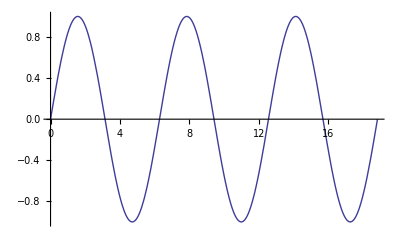

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

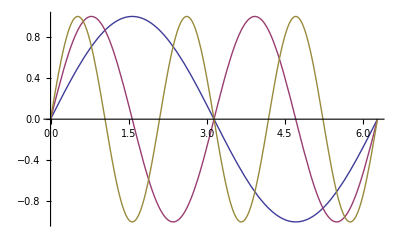

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi}]
```

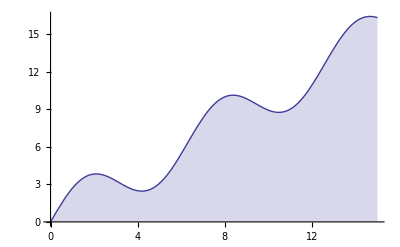

```mathematica
Plot[2Sin[x]+x,{x,0,15},Filling->Bottom]
```

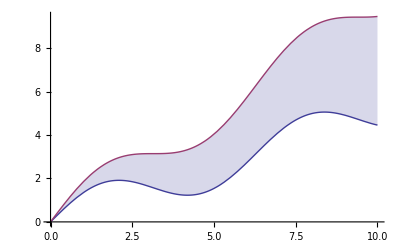

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}}]
```

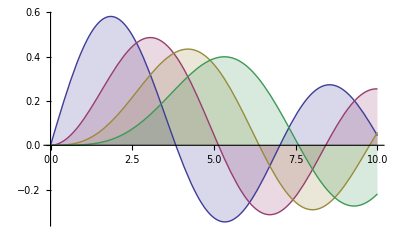

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

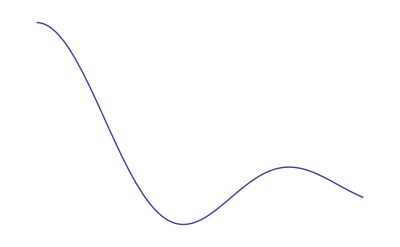

```mathematica
Plot[Sinc[x],{x,0,10},Axes->False]
```

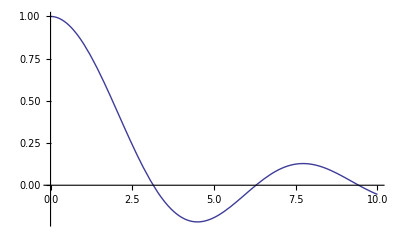

```mathematica
Plot[Sinc[x],{x,0,10},Axes->{False,True}]
```

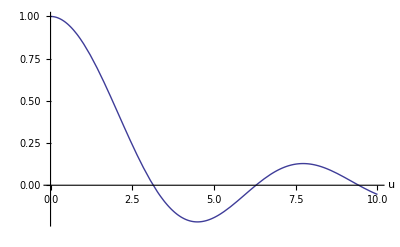

```mathematica
Plot[Sinc[u],{u,0,10},AxesLabel->Automatic]
```

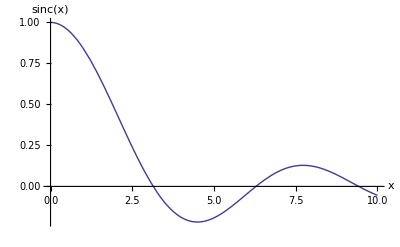

```mathematica
Plot[Sinc[x],{x,0,10},AxesLabel->{x,Sinc[x]}]
```

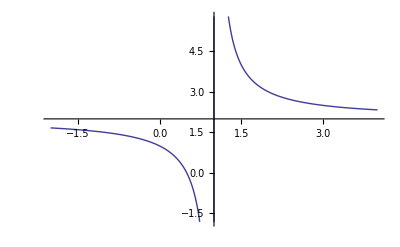

```mathematica
Plot[1/(x-1)+2,{x,-2,4},AxesOrigin->{1,2}]
```

```mathematica
Plot[Sinc[x],{x,0,10},AxesStyle->{Directive[Thick,Dashed,Red],Blue}]
```

-Graphics-

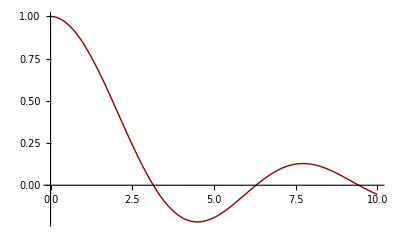

```mathematica
Plot[Sinc[x],{x,0,10},ColorFunction->Function[{x,y},If[y>0,Red,Black]],ColorFunctionScaling->False,PlotStyle->Thick]
```

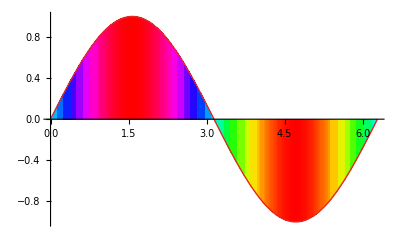

```mathematica
Plot[Sin[x],{x,0,2Pi},ColorFunction->Function[{x,y},Hue[y]],Filling->Axis]
```

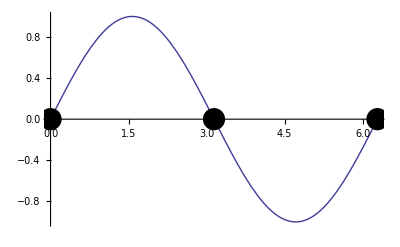

```mathematica
Plot[Sin[x],{x,0,2Pi},Epilog->{PointSize[0.04],Point[{0,0}],Point[{Pi,0}],Point[{2Pi,0}]}]
```

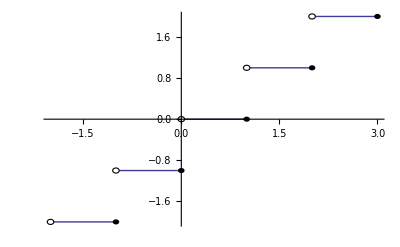

```mathematica
Plot[Floor[x], {x,-2,3}, Epilog-> { Table[{EdgeForm[Black],White,Disk[{i,i},0.05]}, {i,-2,2}], Table[Disk[{i+1,i},0.05],{i,-2,2}]}]
```

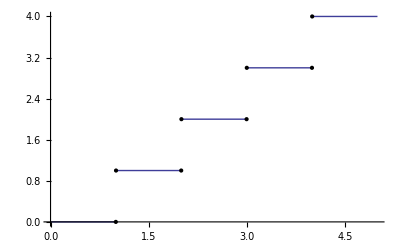

```mathematica
Plot[Floor[x],{x,0,5},ExclusionsStyle->{None,Black}]
```

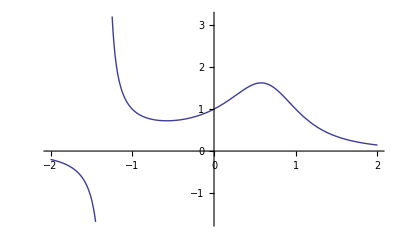

```mathematica
Plot[1/(x^3-x+1),{x,-2,2},Exclusions->{x^3-x+1==0}]
```

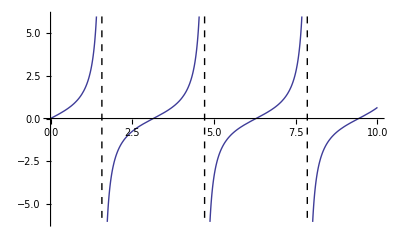

```mathematica
Plot[Tan[x],{x,0,10},Exclusions->{Cos[x]==0},ExclusionsStyle->Dashing[Small]]
```

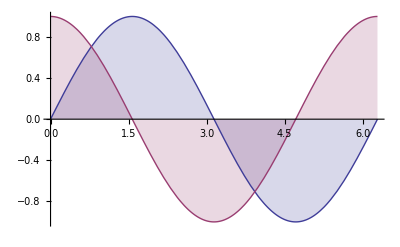

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->Axis]
```

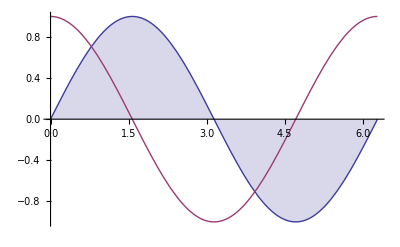

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->Axis}]
```

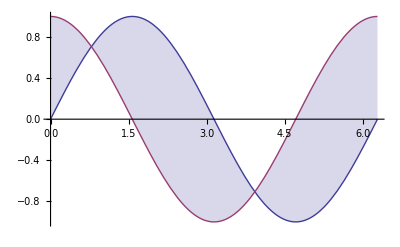

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->{2}}]
```

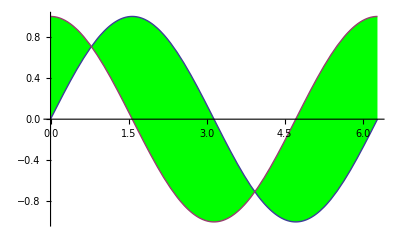

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->{{2},Green}}]
```

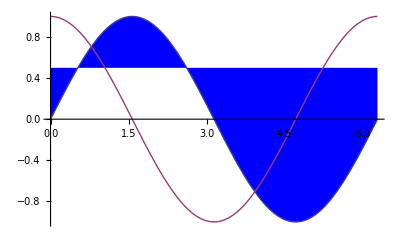

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->{1/2,Blue}}]
```

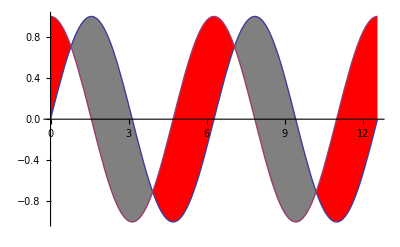

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,4Pi},Filling->{1->{{2},{Red,Gray}}}]
```

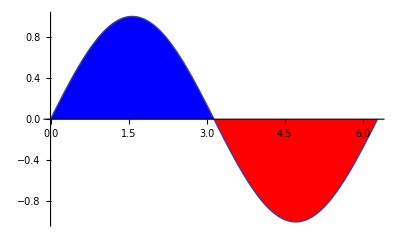

```mathematica
Plot[Sin[x],{x,0,2Pi},Filling->Axis,FillingStyle->{Red,Blue}]
```

```mathematica
Plot[Sin[x],{x,0,2Pi},ColorFunction->Function[{x,y},Hue[y]],Filling->Axis,FillingStyle->Automatic]
```

-Graphics-

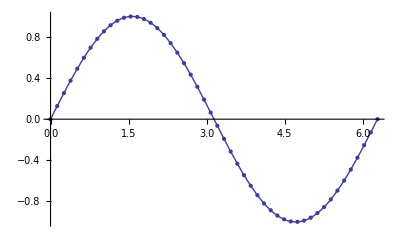

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->Full]
```

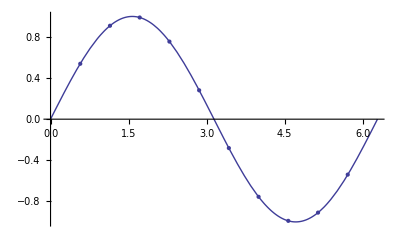

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->10]
```

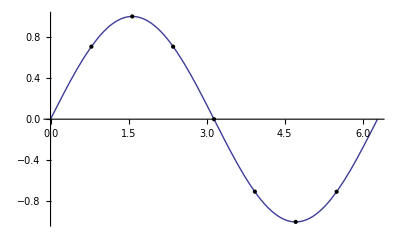

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->{Range[0,2Pi,Pi/4]},MeshStyle->PointSize[Medium]]
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->10,MeshStyle->Automatic]
```

-Graphics-

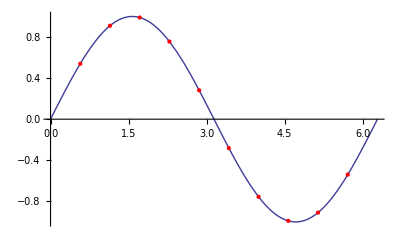

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->10,MeshStyle->Red]
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->10,MeshStyle->Directive[PointSize[Large],Red]]
```

-Graphics-

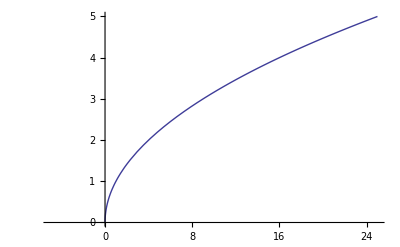

```mathematica
Plot[Sqrt[x],{x,-5,25},PlotRange->Full]
```

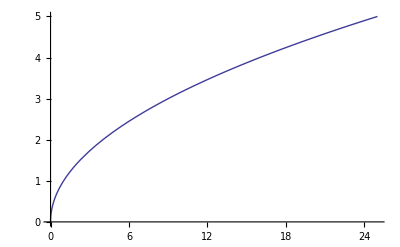

```mathematica
Plot[Sqrt[x],{x,-5,25},PlotRange->Automatic]
```

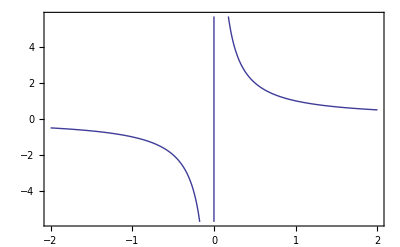

```mathematica
Plot[1/x,{x,-2,2},Frame->True]
```

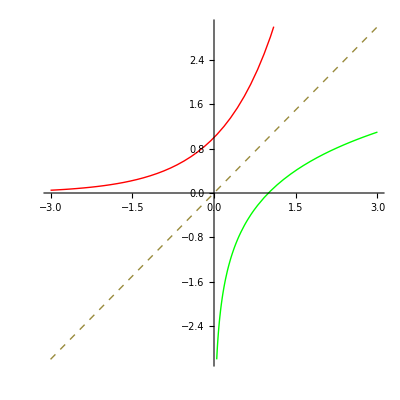

```mathematica
Plot[{Exp[x],Log[x],x},{x,-3,3},PlotRange->3,PlotStyle->{Red,Green,Dashed}, AspectRatio->Automatic]
```

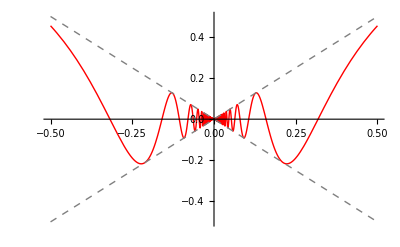

```mathematica
Plot[{x Sin[1/x],Abs[x],-Abs[x]}, {x,-1/2,1/2}, PlotStyle->{Red,Directive[Dashed,Gray],Directive[Dashed,Gray]}]
```

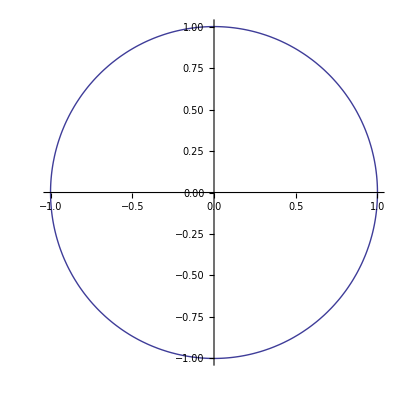
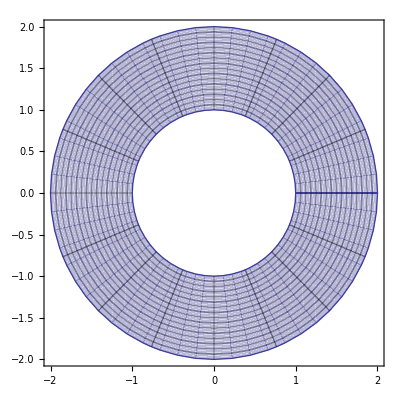

```mathematica
{ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2Pi}],ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2Pi},{r,1,2}]}
```

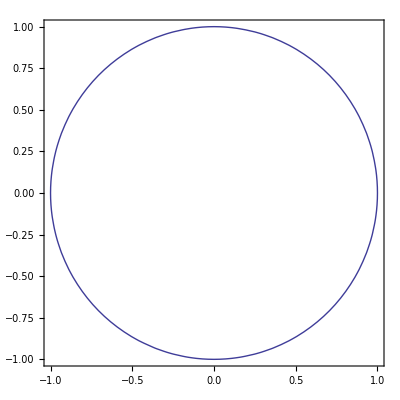
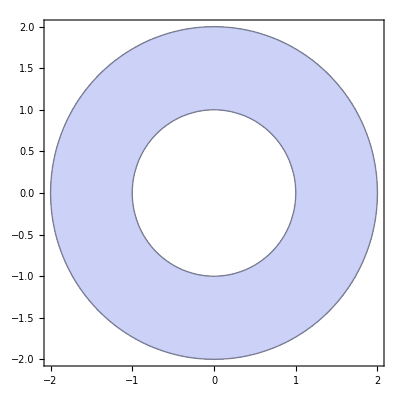

```mathematica
{ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}],RegionPlot[1<x^2+y^2<4,{x,-2,2},{y,-2,2}]}
```

```mathematica
Plot3D[Sin[x^2+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[u^2+v^2],{u,-3,3},{v,-2,2},AxesLabel->{u,v},PlotLabel->Sin[u^2+v^2]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[u v],{u,0,3},{v,0,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Sin[u v],{u,0,3},{v,0,3},AxesLabel->{u,v},PlotLabel->Sin[u v]]
```

-Graphics3D-

```mathematica
Plot3D[1/(x^2+y^2),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[(x^2+y^2)Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{-2 Cos[u] Cos[v]^3,-2 Cos[v]^2 Sin[u],2 Tan[v]},{u,0,2Pi},{v,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x],Cos[x]},{x,0,2Pi},{y,0,2Pi},PlotStyle->{Red,Blue}]
```

-Graphics3D-

```mathematica
ParametricPlot[{Cos[u],Sin[u]},{u,0,2Pi}]
```

-Graphics-

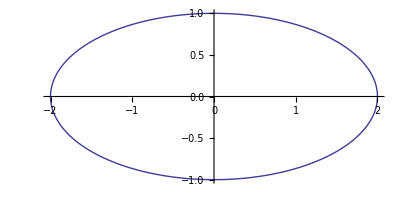

```mathematica
ParametricPlot[{2Cos[u],Sin[u]},{u,0,2Pi}]
```

```mathematica
{x,y}={Cos[u],Sin[u]};
x^2+y^2//Simplify
```

1

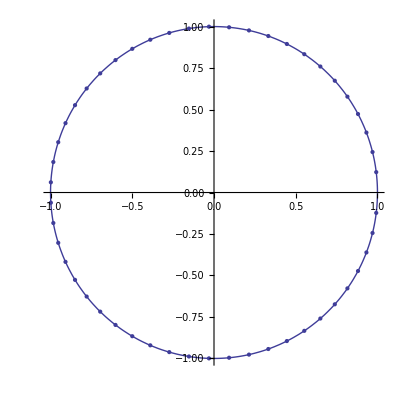

```mathematica
ParametricPlot[Evaluate[{x,y}],{u,0,2Pi},Mesh->50]
```

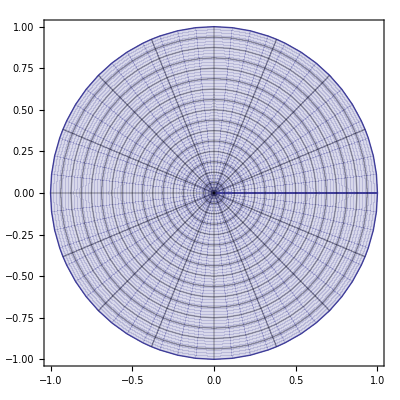

```mathematica
ParametricPlot[{v Cos[u],v Sin[u]},{u,0,2Pi},{v,0,1}]
```

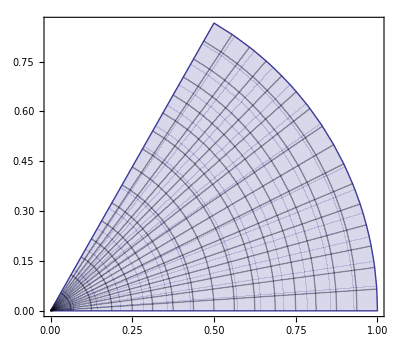

```mathematica
ParametricPlot[{v Cos[u],v Sin[u]},{u,0,Pi/3},{v,0,1}]
```

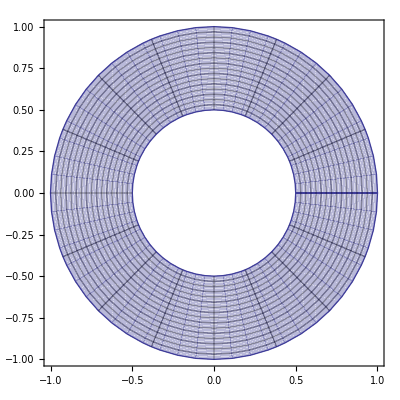

```mathematica
ParametricPlot[{v Cos[u],v Sin[u]},{u,0,2Pi},{v,1/2,1}]
```

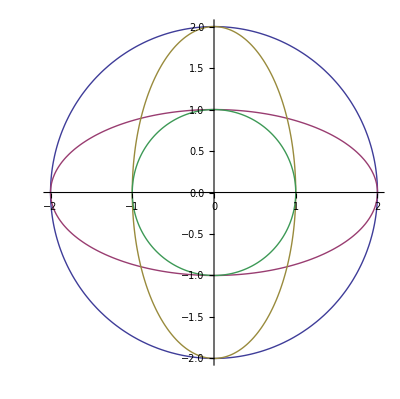

```mathematica
ParametricPlot[{{2Cos[t],2Sin[t]},{2Cos[t],Sin[t]},{Cos[t],2Sin[t]},{Cos[t],Sin[t]}},{t,0,2Pi}]
```

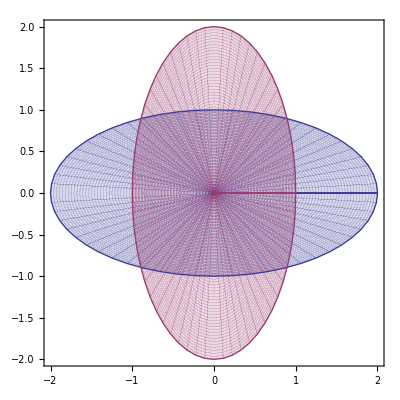

```mathematica
ParametricPlot[{{2r Cos[t],r Sin[t]},{r Cos[t],2r Sin[t]}},{t,0,2Pi},{r,0,1},Mesh->False]
```

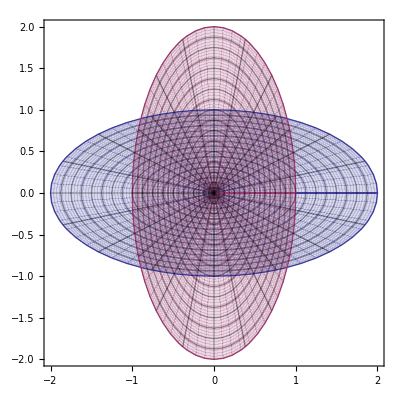

```mathematica
ParametricPlot[{{2r Cos[t],r Sin[t]},{r Cos[t],2r Sin[t]}},{t,0,2Pi},{r,0,1}]
```

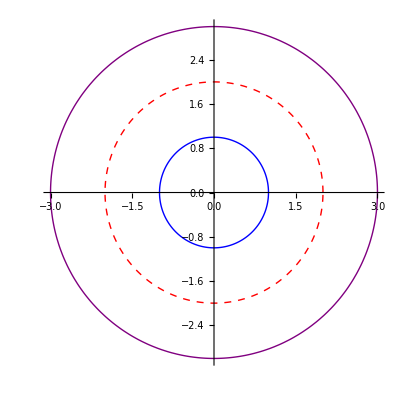

```mathematica
ParametricPlot[Evaluate[Table[{i Cos[u],i Sin[u]},{i,1,3}]],{u,0,2Pi},PlotStyle->{Blue,Directive[Red,Dashed],Directive[Purple,Thick]}]
```

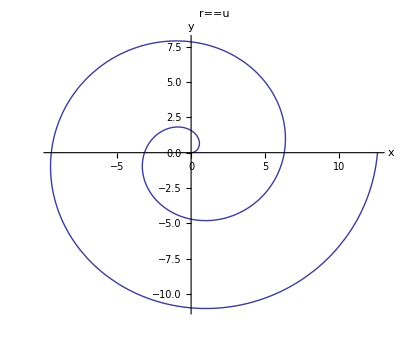

```mathematica
ParametricPlot[{u Cos[u],u Sin[u]},{u,0,4Pi},AxesLabel->{x,y},PlotLabel->r==u]
```

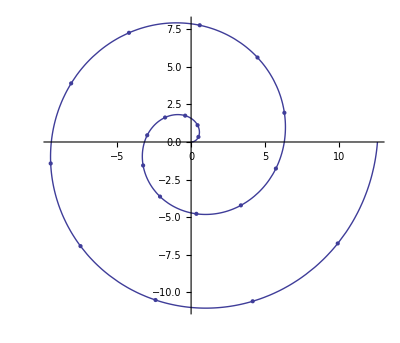

```mathematica
ParametricPlot[{u Cos[u],u Sin[u]},{u,0,4Pi},Mesh->20]
```

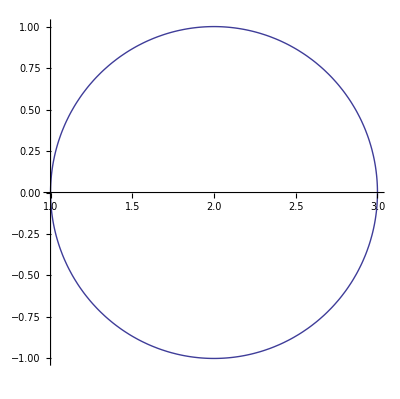

```mathematica
ParametricPlot[{2+Cos[t],Sin[t]},{t,0,2Pi}]
```

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2Pi}]
```

-Graphics3D-

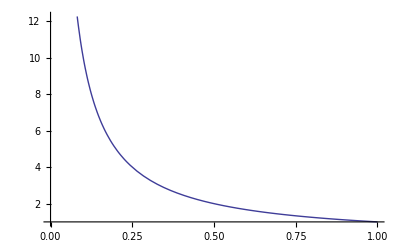

```mathematica
Plot[1/t,{t,0,1},Exclusions->{t==0}]
```

```mathematica
RevolutionPlot3D[1/t,{t,0,1}]
```

-Graphics3D-

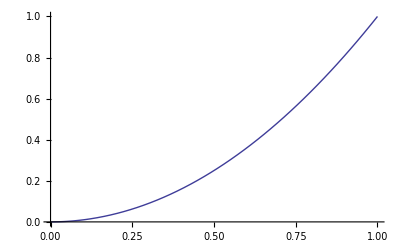

```mathematica
Plot[{t^2},{t,0,1}]
```

```mathematica
RevolutionPlot3D[{t^2},{t,0,1}]
```

-Graphics3D-